```mathematica
LP1 = 1/2({{1, Cos[2θ1], Sin[2θ1], 0}, {Cos[2θ1], Cos[2θ1]^2, Sin[2θ1]Cos[2θ1], 0}, {Sin[2θ1], Sin[2θ1]Cos[2θ1], Sin[2θ1]^2, 0}, {0, 0, 0, 0}})
LP2 = 1/2({{1, Cos[2θ2], Sin[2θ2], 0}, {Cos[2θ2], Cos[2θ2]^2, Sin[2θ2]Cos[2θ2], 0}, {Sin[2θ2], Sin[2θ2]Cos[2θ2], Sin[2θ2]^2, 0}, {0, 0, 0, 0}})
```

{{1/2,1/2 Cos[2 θ1],1/2 Sin[2 θ1],0},{1/2 Cos[2 θ1],1/2 Cos[2 θ1]^2,1/2 Cos[2 θ1] Sin[2 θ1],0},{1/2 Sin[2 θ1],1/2 Cos[2 θ1] Sin[2 θ1],1/2 Sin[2 θ1]^2,0},{0,0,0,0}}

{{1/2,1/2 Cos[2 θ2],1/2 Sin[2 θ2],0},{1/2 Cos[2 θ2],1/2 Cos[2 θ2]^2,1/2 Cos[2 θ2] Sin[2 θ2],0},{1/2 Sin[2 θ2],1/2 Cos[2 θ2] Sin[2 θ2],1/2 Sin[2 θ2]^2,0},{0,0,0,0}}

```mathematica
GQWP=({{1, 0, 0, 0}, {0, Cos[2θ]^2, Sin[2θ]Cos[2θ], Sin[2θ]}, {0, Sin[2θ]Cos[2θ], Sin[2θ]^2, -Cos[2θ]}, {0, -Sin[2θ], Cos[2θ], 0}})
```

{{1,0,0,0},{0,Cos[2 θ]^2,Cos[2 θ] Sin[2 θ],Sin[2 θ]},{0,Cos[2 θ] Sin[2 θ],Sin[2 θ]^2,-Cos[2 θ]},{0,-Sin[2 θ],Cos[2 θ],0}}

```mathematica
LP2*GQWP*LP1
```

{{1/4,0,0,0},{0,1/4 Cos[2 θ]^2 Cos[2 θ1]^2 Cos[2 θ2]^2,1/4 Cos[2 θ] Cos[2 θ1] Cos[2 θ2] Sin[2 θ] Sin[2 θ1] Sin[2 θ2],0},{0,1/4 Cos[2 θ] Cos[2 θ1] Cos[2 θ2] Sin[2 θ] Sin[2 θ1] Sin[2 θ2],1/4 Sin[2 θ]^2 Sin[2 θ1]^2 Sin[2 θ2]^2,0},{0,0,0,0}}

JONES MATRIX

{{Cos[θ]^2+ⅈ Sin[θ]^2,(1-ⅈ) Cos[θ] Sin[θ]},{(1-ⅈ) Cos[θ] Sin[θ],ⅈ Cos[θ]^2+Sin[θ]^2}}

{{1,0},{0,0}}

{1,0}

0

0

{Cos[θ]^2+ⅈ Sin[θ]^2,0}

Abs[Cos[θ]^2+ⅈ Sin[θ]^2]

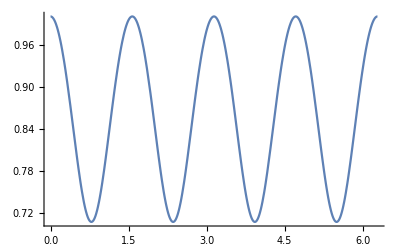

```mathematica
QWP = ({{Cos[θ]^2+ⅈ Sin[θ]^2, (1-ⅈ)Sin[θ]Cos[θ]}, {(1-ⅈ)Sin[θ]Cos[θ], Sin[θ]^2+ⅈ Cos[θ]^2}})
POL=({{Cos[θ2]^2, Sin[θ2]Cos[θ2]}, {Sin[θ2]Cos[θ2], Sin[θ2]^2}})
IncVec = {Cos[θ1],Sin[θ1]}
(*IncVec = ({{Cos[θ1]}, {Sin[θ1]}})*)
θ2=π/180*0
θ1=π/180*0
FinalVector =POL.QWP.IncVec
intensity = Norm[FinalVector]
Plot[intensity,{θ,0,2π}]
```